```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

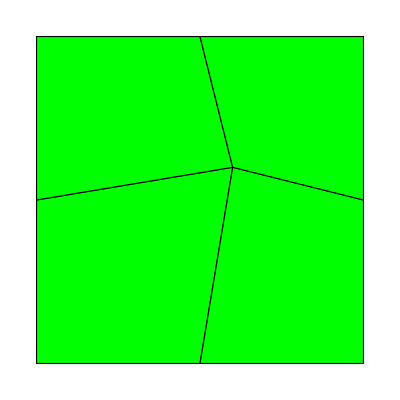

```mathematica
(*Uvozimo elemente ter node*)
Elements = Import["IsoParamData/elements4IP.txt","Table","FieldSeparators"->","];
Nodes = Import["IsoParamData/nodes4IP.txt","Table","FieldSeparators"->","];
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];

(*Prikaz elementov*)
ELplot= Table[{
	Graphics[{Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]]}]},
	{i,1,Length[Elements]}];
Show[ELplot]
```

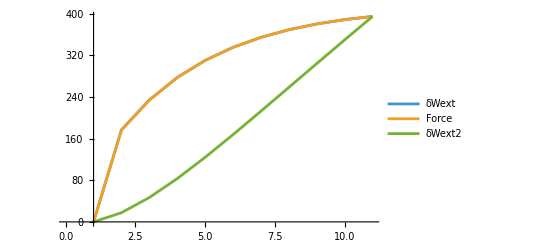

```mathematica
(*Uvoz podatkov -> Sila*)
Force = Import["IsoParamData/Force.txt", "Table", HeaderLines -> 3][[1;;-5,2]];
δWext = 1 * Force;
(*Pomiki ter napetosti*)
U = Import["IsoParamData/Displacement.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];
δWext2 = Force U;

ListLinePlot[{δWext, Force, δWext2}, AxesOrigin->{1,0}, PlotLegends->{"δWext","Force" ,"δWext2"}]
```

```mathematica
(*Uvoz napesti -> kot gradient*)
NAP = Import["IsoParamData/Napetost.JSON", "RawJSON"];
Keys[NAP[["0"]]];
```

```mathematica
(*Uvoz gradientov*)
(*FJSON[frame][element][Gauss Integration Point][Variable -> x,y,F]*)
(*F = FJSON[ToString[frame]][ToString[element]][ToString[integracijsaTocka]]["F"];*)
FJSON = Import["IsoParamData/Grad_4elem_IP_PHANTOM.json","RawJSON"];
FJSON;
```

```mathematica
(*Iteracija po framih*)
Frames = Length[Keys[FJSON]];

nelements = Length[Keys[FJSON[["1"]]]];
ngpoint = Length[Keys[FJSON[["1"]][[ToString[Keys[FJSON[["1"]]][[1]]]]]]];
Δt = 1/(Frames-1) (Frames-1) ;
```

```mathematica
δWint = {}; (*Notranje virtualno delo za vse frame*)


ElementNumbers = Keys[FJSON[[1]]];
(*
1. For -> index ele -> elementi
	2. For -> index gp -> integrac. tocka
*)
For[frame = 1, frame <= Frames, frame ++,
Fframe = FJSON[ ToString[frame-1]];
δWinte = 0;
For[ele=1, ele <= Length[Elements], ele++,
det = {};
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);
x = Nodes[[Elements[[ele]]]][[;;,1]];
y = Nodes[[Elements[[ele]]]][[;;,2]];

X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});


det = Append[det,
{
Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]
}];

(*nele2 =  Keys[FJSON[["1"]]][[ele]];*)
Fele = Fframe[ ToString[ele]];
δWintgp = 0;

For[gp = 1, gp <= 4, gp++,
(*	Print["frame -> ",frame, " N. ele -> ",ele, " gp -> ",gp]; 
	Print[NAP[[ToString[frame]]][[ToString[ele]]][[ToString[gp]]][["S"]]];
	Print["Grad:  ele ", Fele[[ToString[gp]]]["F"]];*)
	
	F =  Fele[[ToString[gp]]]["F"];
	F11 = F[[1]];
	F12 = F[[2]];
	F21 = F[[3]];
	F22 = F[[4]];
	F33 = F[[5]];
	F2 = ({{F11, F12, 0}, {F21, F22, 0}, {0, 0, F33}});

	(*Napetosti*)
	σ = NAP[[ToString[frame-1]]][[ToString[ele]]][[ToString[gp]]][["S"]];
	(*σ -> S11, S22, S33, S12*)
	σ11 =σ[[1]];
	σ12 =σ[[4]]; (*Drugi stolpec*)
	σ22 =σ[[2]];
	σ2 = ({{σ11, σ12, 0}, {σ12, σ22, 0}, {0, 0, 0}});
	
	(*δv -> Ḟ*)
	Fdot =FJSON[ToString[Keys[FJSON][[-1]]]][ToString[ElementNumbers[[ele]]]][ToString[gp]]["F"];
	δvf = 1/Δt (Fdot - {1,1,1,1,1});
	(*Print[δvf];*)
	δv11 = δvf[[1]];
	δv12 = δvf[[2]];
	δv21 = δvf[[3]];
	δv22 = δvf[[4]];
	δv33 = δvf[[5]];

			
	(*1. Piola-Kirchoff Stress -> p*)
	p11 = F33 (F22 σ11 - F12 σ12);
	p12 = - F21 F33 σ11 + F11 F33 σ12;
	p21 = F33 (F22 σ12 - F12 σ22);
	p22 = -F21 F22 σ12 + F11 F33 σ22;
			
	(*Print[δWinti]*)
	δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22) *det[[1,gp]];
	(*Print[Total@det[[1,;;]]];*)
	δWintgp += δW; (*Sum dela vseh gaussovih tock*)
	];
	δWinte += δWintgp;
];
δWint = Append[δWint, δWinte];
];
```

```mathematica
δWint
```

{0.,176.606,233.996,277.228,310.071,335.145,354.319,368.947,380.037,388.341,394.436}

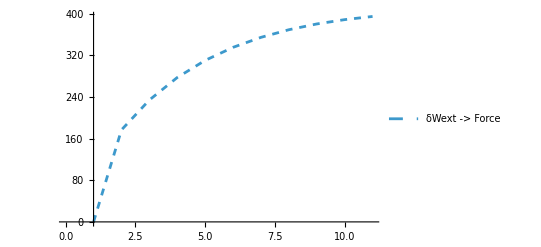

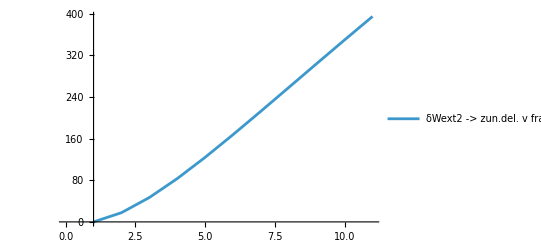

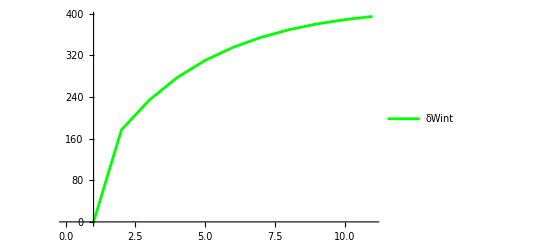

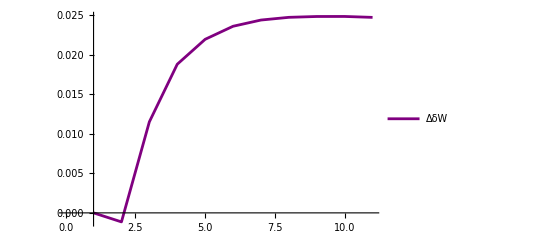

```mathematica
ListLinePlot[{δWext, δWext2, δWint},AxesOrigin->{1,0}, PlotLegends->{"δWext","δWext2","δWint"}, PlotStyle->{Dashed, Dashed, Red}];

P1 = ListLinePlot[{δWext},AxesOrigin->{1,0}, PlotLegends->{"δWext -> Force"}, PlotStyle->Dashed]
P2 = ListLinePlot[{ δWext2},AxesOrigin->{1,0}, PlotLegends->{"δWext2 -> zun.del. v frame"}, PlotStyle->{Normal, Blue}]
P3 = ListLinePlot[{ δWint},AxesOrigin->{1,0}, PlotLegends->{"δWint"}, PlotStyle->Green]
P4 = ListLinePlot[{(δWext - δWint)},AxesOrigin->{1,0}, PlotLegends->{"ΔδW"}, PlotStyle->Purple]
```

```mathematica
{δWext,δWext2, δWint}
```

{{0.,176.604,234.007,277.247,310.093,335.169,354.343,368.972,380.061,388.366,394.46},{0.,17.6604,46.8014,83.174,124.037,167.585,212.606,258.281,304.049,349.529,394.46},{0.,176.606,233.996,277.228,310.071,335.145,354.319,368.947,380.037,388.341,394.436}}

```mathematica
(δWext -  δWint)/(δWint + 10^-16)
```

{0.,-6.46424×10^-6,0.0000492287,0.0000678501,0.00007084,0.0000704655,0.0000688757,0.000067074,0.0000653964,0.0000640088,0.0000627241}

```mathematica
(δWint+10^-16) / (δWext + 10^-16)
```

{1.,1.00001,0.999951,0.999932,0.999929,0.99993,0.999931,0.999933,0.999935,0.999936,0.999937}